# First Lyapunov coefficient on the Hopf curve of the four-stage SIS model

This notebook derives, step by step, the closed form (9)-(10) of the draft for the first Lyapunov coefficient l_1 along the Hopf set of the four-stage SIS model (n = 4, q = 1). It uses Kuznetsov's invariant formula (Yu. A. Kuznetsov, Andronov-Hopf bifurcation, Scholarpedia 1(10):1858, 2006; Elements of Applied Bifurcation Theory, 3rd ed., Sec. 3.5)

## 0. Setup

All symbols (ω, p, a, b, m) are real, and ω > 0 is the frequency. Every complex quantity in this notebook is a rational function of iω with real coefficients (the parameters on the Hopf curve depend on ω^2 only). Its complex conjugate is therefore obtained by replacing ω ωith -ω; cc does that. (This avoids Conjugate[ω] for a symbolic ω; a numerical check against Conjugate follows in Section 5.)

```mathematica
ClearAll["Global`*"];
```

```mathematica
cc[z_] := z /. ω -> -ω;
```

## 1. The model and the Jacobian at the endemic equilibrium

Model (1) with n = 4, q = 1; b stands for beta. The endemic equilibrium is (2).

```mathematica
vars = {i1, i2, i3, i4};
```

```mathematica
rhs = {b i1 (1 - i1 - i2 - i3 - i4) - p i1, p i1 - i2, i2 - i3, i3 - i4};
```

```mathematica
ee = {i1 -> (b - p)/(b (3 p + 1)), i2 -> p (b - p)/(b (3 p + 1)),
      i3 -> p (b - p)/(b (3 p + 1)), i4 -> p (b - p)/(b (3 p + 1))};
```

```mathematica
Simplify[rhs /. ee]
```

{0,0,0,0}

The Jacobian at the equilibrium. With a = b I1* = (b - p)/(3 p + 1), i.e. b = p + a (3 p + 1), it is the matrix A of (4).

```mathematica
J = Table[D[rhs[[k]], v], {k, 4}, {v, vars}];
```

```mathematica
A = Simplify[J /. ee /. b -> p + a (3 p + 1)]
```

{{-a,-a,-a,-a},{p,-1,0,0},{0,1,-1,0},{0,0,1,-1}}

Check

```mathematica
A == {{-a, -a, -a, -a}, {p, -1, 0, 0}, {0, 1, -1, 0}, {0, 0, 1, -1}}
```

True

## 2. Characteristic polynomial, Hurwitz determinants, Hopf condition (Theorem 3(a))

```mathematica
chi = Expand[Det[lam IdentityMatrix[4] - A]];
```

```mathematica
{a0, a1, a2, a3} = Most[CoefficientList[chi, lam]]
```

{a+3 a p,1+3 a+3 a p,3+3 a+a p,3+a}

```mathematica
Expand[chi - ((lam + a) (lam + 1)^3 + a p (lam^2 + 3 lam + 3))]
```

0

Hurwitz determinants: Delta2 = a3 a2 - a1 is positive; stability is decided by Delta3 = a3 a2 a1 - a1^2 - a3^2 a0.

```mathematica
Delta2 = Expand[a3 a2 - a1]
```

8+9 a+3 a^2+a^2 p

```mathematica
Delta3 = Expand[a3 a2 a1 - a1^2 - a3^2 a0];
```

```mathematica
Expand[Delta3 - (3 a^3 p^2 + a (9 a^2 + 10 a - 3) p + 8 (1 + a)^3)]
```

0

(3p+1)^3 Delta3, written in b and p, is the polynomial f(b, p) of (6):

```mathematica
fpaper = (3 p^2 + 9 p + 8) b^3 + (-9 p^3 + 3 p^2 + 58 p + 24) b^2 +
   (9 p^4 - 60 p^3 + 58 p^2 + 93 p + 24) b - 3 p^5 + 48 p^4 + 92 p^3 + 99 p^2 + 48 p + 8;
```

## 3. The Hopf curve, parametrized by s = ω^2 (Theorem 3(c))

Put lam = i ω and z = 1 + i ω then chi(i ω) = (i ω + a) z^3 + a p (z^2 + z + 1). With m = a p this is linear in (a, m); its real and imaginary parts give two linear equations.

```mathematica
z = 1 + I ω;
```

```mathematica
chiH = Expand[(I ω + a) z^3 + m (z^2 + z + 1)];
```

```mathematica
re = Expand[(chiH + cc[chiH])/2];
```

```mathematica
im = Expand[(chiH - cc[chiH])/(2 I)];
```

```mathematica
{Collect[re /. ω -> Sqrt[s], {a, m}], Collect[Expand[im/ω] /. ω -> Sqrt[s], {a, m}]}
```

{a (1-3 s)+m (3-s)-3 s+s^2,1+3 m+a (3-s)-3 s}

These are (1 - 3s) a + (3 - s) a p = s (3 - s) and (3 - s) a + 3 a p = 3 s - 1 (moved to one side). Solve the linear system:

```mathematica
solHopf = Simplify[Solve[{re == 0, im == 0}, {a, m}]]
```

{{a→(-3+ω^2)/(6+3 ω^2+ω^4),m→((1+ω^2)^3)/(6+3 ω^2+ω^4)}}

So a = (s - 3)/(s^2 + 3 s + 6), a p = (s + 1)^3/(s^2 + 3 s + 6), p = (s + 1)^3/(s - 3), and b = p + a (3 p + 1), as in (7). From now on these are written with s = ω^2:

```mathematica
aH = (ω^2 - 3)/(ω^4 + 3 ω^2 + 6);
```

```mathematica
pH = (ω^2 + 1)^3/(ω^2 - 3);
```

```mathematica
bH = Together[pH + aH (3 pH + 1)];
```

```mathematica
Together[{a, m} - {aH, aH pH} /. First[solHopf]]
```

{0,0}

Checks: the form of beta(s) in (7); f(beta(s), p(s)) = 0; Delta3 = 0; and ω^2 = a1/a3 (Theorem 3(b)).

```mathematica
Together[bH - (pH + ω^2 (3 ω^4 + 9 ω^2 + 10)/(ω^4 + 3 ω^2 + 6))]
```

0

```mathematica
Together[fpaper /. {b -> bH, p -> pH}]
```

0

```mathematica
Together[Delta3 /. {a -> aH, p -> pH}]
```

0

```mathematica
Together[(a1/a3 /. {a -> aH, p -> pH}) - ω^2]
```

0

## 4. The ingredients of Kuznetsov's formula at a point of the Hopf curve

The Jacobian on the curve, and the eigenvector q with A q = i ω q, normalised by q1 = 1 (rows 2-4 of A q = i ω q give q_{k+1} = q_k/(1 + i ω) times p for k = 1, then 1 for k = 2, 3).

```mathematica
AH = A /. {a -> aH, p -> pH};
```

```mathematica
q = {1, pH/(1 + I ω), pH/(1 + I ω)^2, pH/(1 + I ω)^3};
```

```mathematica
Together[AH . q - I ω q]
```

{0,0,0,0}

The adjoint eigenvector: A^T pv = -i ω pv with <pv, q> = conj(pv).q = 1. We compute pb = conj(pv) instead, which satisfies A^T pb = i ω pb and pb.q = 1; then <pv, x> = pb.x for every x. Rows 2-4 and the normalisation determine pb; row 1 is checked afterwards.

```mathematica
pbVars = {u1, u2, u3, u4};
```

```mathematica
eqs = Thread[(Transpose[AH] - I ω IdentityMatrix[4]) . pbVars == 0];
```

```mathematica
pb = Together[pbVars /. First[Solve[Append[Rest[eqs], pbVars . q == 1], pbVars]]];
```

```mathematica
pb
```

{(-6 ⅈ+6 ω-3 ⅈ ω^2+3 ω^3-ⅈ ω^4+ω^5)/(2 ω (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4)),((-3 ⅈ+3 ω+ⅈ ω^2) (-3+ω^2))/(2 ω (-ⅈ+ω)^2 (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4)),((2+ⅈ ω) (-3+ω^2))/(2 ω (-ⅈ+ω) (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4)),(ⅈ (-3+ω^2))/(2 ω (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4))}

```mathematica
{Together[Transpose[AH] . pb - I ω pb], Together[pb . q]}
```

{{0,0,0,0},1}

```mathematica
hess = Table[D[rhs[[k]], {vars, 2}], {k, 4}];
```

```mathematica
hess[[1]]
```

{{-2 b,-b,-b,-b},{-b,0,0,0},{-b,0,0,0},{-b,0,0,0}}

```mathematica
Bgen[x_, y_] := Table[x . hess[[k]] . y, {k, 4}];
```

```mathematica
B[x_, y_] := Bgen[x, y] /. b -> bH;
```

Check

```mathematica
Expand[Bgen[{x1, x2, x3, x4}, {y1, y2, y3, y4}] -
  {-b (x1 (y1 + y2 + y3 + y4) + y1 (x1 + x2 + x3 + x4)), 0, 0, 0}]
```

{0,0,0,0}

Since B has only a first component, <p, B(x, y)> = pb[[1]] B1(x, y): only the first component of the adjoint vector enters the formula. It is

```mathematica
Factor[pb[[1]]]
```

((-ⅈ+ω) (6+3 ω^2+ω^4))/(2 ω (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4))

## 5. The three terms of the formula

h11 = A^-1 B(q, qbar) and h20 = (2 i ω I - A)^-1 B(q, q). Then G = - 2 <p, B(q, h11)> + <p, B(qbar, h20)>, because C(q,q,qbar) is 0.

```mathematica
qb = cc[q];
```

```mathematica
Chop[N[(qb - Conjugate[q /. ω -> 27/10]) /. ω -> 27/10]]
```

{0,0,0,0}

```mathematica
h11 = Together[LinearSolve[AH, B[q, qb]]];
```

```mathematica
h20 = Together[LinearSolve[2 I ω IdentityMatrix[4] - AH, B[q, q]]];
```

```mathematica
G = Together[pb . (-2 B[q, h11] + B[qb, h20])];
```

## 6. l_1 = Re G/(2 ω), and comparison with (9)-(10)

```mathematica
l1 = Factor[Together[(G + cc[G])/2]/(2 ω)]
```

((-ⅈ+ω) (ⅈ+ω) (6+3 ω^2+ω^4) (6-9 ω^2+11 ω^4+18 ω^6+9 ω^8+ω^10)^2 (-100-540 ω^2-975 ω^4-537 ω^6-117 ω^8-15 ω^10+4 ω^12))/(2 ω (-3+ω^2)^4 (10-5 ⅈ ω+3 ω^2-ⅈ ω^3+ω^4) (10+5 ⅈ ω+3 ω^2+ⅈ ω^3+ω^4) (-10-30 ⅈ ω+15 ω^2-20 ⅈ ω^3+9 ω^4-6 ⅈ ω^5+4 ω^6) (-10+30 ⅈ ω+15 ω^2+20 ⅈ ω^3+9 ω^4+6 ⅈ ω^5+4 ω^6))

The formula of the draft, with s = ω^2 and Sqrt[s] = ω (ω > 0):

```mathematica
P4[s_] := s^4 + 7 s^3 + 39 s^2 + 85 s + 100;
```

```mathematica
P5[s_] := s^5 + 9 s^4 + 18 s^3 + 11 s^2 - 9 s + 6;
```

```mathematica
P6[s_] := 16 s^6 + 108 s^5 + 441 s^4 + 950 s^3 + 1245 s^2 + 600 s + 100;
```

```mathematica
gg[s_] := 4 s^6 - 15 s^5 - 117 s^4 - 537 s^3 - 975 s^2 - 540 s - 100;
```

```mathematica
l1paper[s_, ω_] := (s + 1) (s^2 + 3 s + 6) P5[s]^2 gg[s]/(2 ω (s - 3)^4 P4[s] P6[s]);
```

```mathematica
Together[l1 - l1paper[ω^2, ω]]
```

0

## 7. The sign of l1 is the sign of g(s)

P4 and P6 have positive coefficients. P5 has one negative coefficient but is positive for s > 3:

```mathematica
{CoefficientList[P4[s], s], CoefficientList[P6[s], s]}
```

{{100,85,39,7,1},{100,600,1245,950,441,108,16}}

```mathematica
Reduce[P5[s] <= 0 && s > 3, s]
```

False

The other factors s + 1, s^2 + 3 s + 6, (s - 3)^4, ω are positive, so sign l_1 = sign g(s). g is irreducible over Q, and its coefficients change sign exactly once, so  g has exactly one positive root s*; since g(3) < 0 it lies in (3, oo):

```mathematica
FactorList[gg[s]]
```

{{1,1},{-100-540 s-975 s^2-537 s^3-117 s^4-15 s^5+4 s^6,1}}

```mathematica
CoefficientList[gg[s], s]
```

{-100,-540,-975,-537,-117,-15,4}

```mathematica
gg[3]
```

-35200

```mathematica
CountRoots[gg[s], {s, 3, 250}]
```

1

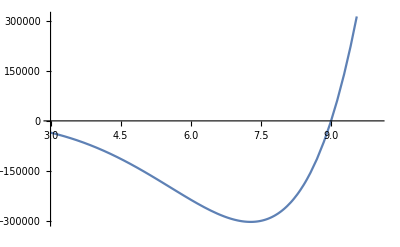

```mathematica
Plot[gg[s],{s,3,10}]
```

```mathematica
sStar = s /. FindRoot[gg[s] == 0, {s, 9}, WorkingPrecision -> 40]
```

9.006904547551498529769611034277644728592

## 8. The Bautin (generalised Hopf) point

```mathematica
ωStar = Sqrt[sStar];
```

```mathematica
{pStar, bStar} = {pH, bH} /. ω -> ωStar;
```

```mathematica
N[{sStar, pStar, bStar, ωStar, bStar/pStar}, 15]
```

{9.0069045475515,166.820162838508,193.209616162024,3.00115053730257,1.15819102963628}

Expected: s* = 9.00690454755150, p* = 166.820162838508, beta* = 193.209616162024, ω* = 3.00115053730257, R0* = 1.15819102963628.